```mathematica
p6=MatrixFromGraph[PathGraph[Range[6]]]//GraphMatrixSignature
```

4802905

```mathematica
gr6=Select[Keys[allGraphs6],allGraphs6[#,"comp"]===Greater&&IsomorphicGraphQ[allGraphs6[#,"graph"],PathGraph[Range[6]]]&];
```

```mathematica
Clear[RepComp6];RepComp6[base_]:=RepComp6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->allGraphs6[key,"comp"],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Length[Select[ListofVars[allGraphs6[6383937,"colofour"]]/.RepComp6["C"],#===Greater&]]
```

3

```mathematica
Table[{Length[Select[ListofVars[allGraphs6[k,"colofour"]]/.RepComp6["C"],#===Greater&]],k},{k,gr6}]//Sort
```

{{0,78985},{0,79713},{0,81163},{0,81165},{0,85303},{0,85375},{0,197803},{0,197811},{0,256125},{0,256131},{0,551863},{0,552097},{0,610255},{0,610417},{0,1595305},{0,1614745},{0,1654353},{0,1655803},{0,1655811},{0,1659943},{0,1660177},{0,1673065},{0,4783951},{0,4789567},{0,4802689},{0,4802737},{0,4802899},{0,4802905},{0,4842271},{0,4842297},{0,4842343},{0,4842345},{0,4844451},{0,4844457},{0,4848615},{0,4848661},{0,4848669},{0,4848823},{0,4861711},{0,4861713},{0,4861785},{0,4861791},{0,4861945},{0,4861953},{0,4960395},{0,4961097},{0,4979811},{0,4979835},{0,4980043},{0,4980045},{0,5334103},{0,5334175},{0,6377545},{0,6383863},{1,61515},{1,62217},{1,65935},{1,68041},{1,78825},{1,79551},{1,80931},{1,80955},{1,85329},{1,85377},{1,178155},{1,197077},{1,197571},{1,197643},{1,199263},{1,237177},{1,255915},{1,255963},{1,256617},{1,256851},{1,258309},{1,262449},{1,551161},{1,553555},{1,592921},{1,597133},{1,610209},{1,610263},{1,610911},{1,612361},{1,612369},{1,612603},{1,616735},{1,728515},{1,729243},{1,1597491},{1,1600921},{1,1601695},{1,1601857},{1,1620577},{1,1660017},{1,1660023},{1,1660671},{1,1662121},{1,1673067},{1,1675251},{1,1679617},{1,1679625},{1,1772443},{1,1772445},{1,1778769},{1,1791891},{1,2126503},{1,2145457},{1,4783977},{1,4784023},{1,4785403},{1,4785427},{1,4785435},{1,4789615},{1,4789801},{1,4789855},{1,4802691},{1,4802745},{1,4842111},{1,4842135},{1,4844241},{1,4844289},{1,4844475},{1,4844529},{1,4848687},{1,4848903},{1,4960363},{1,4960387},{1,4960443},{1,4961091},{1,4966761},{1,4966921},{1,4979803},{1,4979829},{1,5314447},{1,5314681},{1,5314735},{1,5315383},{1,5316841},{1,5334097},{1,5334121},{1,5334129},{1,5334177},{1,6377329},{1,6377539},{1,6378031},{1,6378265},{1,6378273},{1,6379723},{1,6383935},{2,61563},{2,65727},{2,66429},{2,184473},{2,184681},{2,196869},{2,203427},{2,238629},{2,242793},{2,258069},{2,262443},{2,262521},{2,532495},{2,538813},{2,551209},{2,551937},{2,551943},{2,557767},{2,610983},{2,616815},{2,709561},{2,729001},{2,729081},{2,1596757},{2,1597485},{2,1603315},{2,1614747},{2,1654191},{2,1655571},{2,1655643},{2,1656297},{2,1656531},{2,1662123},{2,1662363},{2,1675245},{2,1773903},{2,1778067},{2,1778275},{2,1791165},{2,2126575},{2,2146177},{2,2146185},{2,4784025},{2,4785483},{2,4789647},{2,4960155},{2,4960881},{2,4961115},{2,4961169},{2,4966705},{2,4966707},{2,4966785},{2,4966947},{2,5314495},{2,5315221},{2,6377377},{2,6379725},{2,6383857},{2,6383881},{2,6383889},{3,67881},{3,178203},{3,180309},{3,183979},{3,203475},{3,242841},{3,262467},{3,533899},{3,553347},{3,591309},{3,592713},{3,612387},{3,728355},{3,729003},{3,1600969},{3,1601649},{3,1601703},{3,1616205},{3,1660743},{3,1662201},{3,1772211},{3,1772235},{3,1774629},{3,1778761},{3,1779003},{3,1791885},{3,2132407},{3,2133055},{3,4789641},{3,4960227},{3,4960929},{3,5315463},{3,5316625},{3,5316867},{3,6379483},{3,6383937},{5,62289},{5,66663},{5,68067},{5,203395},{5,203419},{5,237249},{5,238653},{5,243027},{5,243081},{5,243729},{5,245187},{5,553315},{5,557713},{5,591543},{5,593001},{5,593649},{5,728299},{5,734833},{5,1616197},{5,1620571},{5,1791157},{5,1797715},{5,2145451},{5,2147635},{5,4783791},{5,4783815},{5,4785195},{5,5314527},{5,5315175},{5,5315229},{5,6377331},{5,6377385},{5,6378033},{5,6378111},{5,6379491},{5,6379515},{6,67905},{6,180333},{6,183819},{6,184761},{6,199047},{6,243567},{6,597159},{6,599319},{6,709401},{6,709587},{6,711747},{6,728301},{6,730461},{6,1595145},{6,1597275},{6,1603099},{6,1603155},{6,1774389},{6,1778035},{6,1778787},{6,1797717},{6,2126529},{6,2128689},{6,2132353},{6,2133135},{6,2134513},{6,4785267},{6,5314521},{6,5316681},{6,6378105},{7,184545},{7,186165},{7,244971},{7,532287},{7,534393},{7,534627},{7,534681},{7,540217},{7,553341},{7,592785},{7,593487},{7,599265},{7,711045},{7,715177},{7,715959},{7,730485},{7,734859},{7,1596549},{7,1597323},{7,1778061},{7,1780221},{7,2126577},{7,2127955},{7,2127979},{7,2127987},{7,2147637},{7,5315247},{7,5316627},{7,5316705},{7,6379509},{9,185925},{9,534441},{9,538839},{9,709425},{9,715257},{9,715905},{9,1603101},{9,1773687},{9,1780245},{9,2128035},{9,2128683},{9,2128761},{11,533739},{11,540297},{11,710805},{11,711531},{11,2128707},{11,2134539}}

```mathematica
allGraphs6[5395609,"atleast"]
```

1

```mathematica
Table[base->(allGraphs6[78985,Bases6[base,"Colofour"]]/.RepGraph6[base]//Expand//Length),{base,Keys[Bases6]}]
```

{C→52,E→32,G→34,F→202}

```mathematica
Map[Labeled[allGraphs6[#[[2]],"graph"],{#[[2]],#[[1]]}]&,Sort[Table[{Length[Select[ListofVars[allGraphs6[k,"colofour"]]/.RepComp6["C"],#===Greater&]],k},{k,gr6}]]]
```

{-Graphics-{78985,0},-Graphics-{79713,0},-Graphics-{81163,0},-Graphics-{81165,0},-Graphics-{85303,0},-Graphics-{85375,0},-Graphics-{197803,0},-Graphics-{197811,0},-Graphics-{256125,0},-Graphics-{256131,0},-Graphics-{551863,0},-Graphics-{552097,0},-Graphics-{610255,0},-Graphics-{610417,0},-Graphics-{1595305,0},-Graphics-{1614745,0},-Graphics-{1654353,0},-Graphics-{1655803,0},-Graphics-{1655811,0},-Graphics-{1659943,0},-Graphics-{1660177,0},-Graphics-{1673065,0},-Graphics-{4783951,0},-Graphics-{4789567,0},-Graphics-{4802689,0},-Graphics-{4802737,0},-Graphics-{4802899,0},-Graphics-{4802905,0},-Graphics-{4842271,0},-Graphics-{4842297,0},-Graphics-{4842343,0},-Graphics-{4842345,0},-Graphics-{4844451,0},-Graphics-{4844457,0},-Graphics-{4848615,0},-Graphics-{4848661,0},-Graphics-{4848669,0},-Graphics-{4848823,0},-Graphics-{4861711,0},-Graphics-{4861713,0},-Graphics-{4861785,0},-Graphics-{4861791,0},-Graphics-{4861945,0},-Graphics-{4861953,0},-Graphics-{4960395,0},-Graphics-{4961097,0},-Graphics-{4979811,0},-Graphics-{4979835,0},-Graphics-{4980043,0},-Graphics-{4980045,0},-Graphics-{5334103,0},-Graphics-{5334175,0},-Graphics-{6377545,0},-Graphics-{6383863,0},-Graphics-{61515,1},-Graphics-{62217,1},-Graphics-{65935,1},-Graphics-{68041,1},-Graphics-{78825,1},-Graphics-{79551,1},-Graphics-{80931,1},-Graphics-{80955,1},-Graphics-{85329,1},-Graphics-{85377,1},-Graphics-{178155,1},-Graphics-{197077,1},-Graphics-{197571,1},-Graphics-{197643,1},-Graphics-{199263,1},-Graphics-{237177,1},-Graphics-{255915,1},-Graphics-{255963,1},-Graphics-{256617,1},-Graphics-{256851,1},-Graphics-{258309,1},-Graphics-{262449,1},-Graphics-{551161,1},-Graphics-{553555,1},-Graphics-{592921,1},-Graphics-{597133,1},-Graphics-{610209,1},-Graphics-{610263,1},-Graphics-{610911,1},-Graphics-{612361,1},-Graphics-{612369,1},-Graphics-{612603,1},-Graphics-{616735,1},-Graphics-{728515,1},-Graphics-{729243,1},-Graphics-{1597491,1},-Graphics-{1600921,1},-Graphics-{1601695,1},-Graphics-{1601857,1},-Graphics-{1620577,1},-Graphics-{1660017,1},-Graphics-{1660023,1},-Graphics-{1660671,1},-Graphics-{1662121,1},-Graphics-{1673067,1},-Graphics-{1675251,1},-Graphics-{1679617,1},-Graphics-{1679625,1},-Graphics-{1772443,1},-Graphics-{1772445,1},-Graphics-{1778769,1},-Graphics-{1791891,1},-Graphics-{2126503,1},-Graphics-{2145457,1},-Graphics-{4783977,1},-Graphics-{4784023,1},-Graphics-{4785403,1},-Graphics-{4785427,1},-Graphics-{4785435,1},-Graphics-{4789615,1},-Graphics-{4789801,1},-Graphics-{4789855,1},-Graphics-{4802691,1},-Graphics-{4802745,1},-Graphics-{4842111,1},-Graphics-{4842135,1},-Graphics-{4844241,1},-Graphics-{4844289,1},-Graphics-{4844475,1},-Graphics-{4844529,1},-Graphics-{4848687,1},-Graphics-{4848903,1},-Graphics-{4960363,1},-Graphics-{4960387,1},-Graphics-{4960443,1},-Graphics-{4961091,1},-Graphics-{4966761,1},-Graphics-{4966921,1},-Graphics-{4979803,1},-Graphics-{4979829,1},-Graphics-{5314447,1},-Graphics-{5314681,1},-Graphics-{5314735,1},-Graphics-{5315383,1},-Graphics-{5316841,1},-Graphics-{5334097,1},-Graphics-{5334121,1},-Graphics-{5334129,1},-Graphics-{5334177,1},-Graphics-{6377329,1},-Graphics-{6377539,1},-Graphics-{6378031,1},-Graphics-{6378265,1},-Graphics-{6378273,1},-Graphics-{6379723,1},-Graphics-{6383935,1},-Graphics-{61563,2},-Graphics-{65727,2},-Graphics-{66429,2},-Graphics-{184473,2},-Graphics-{184681,2},-Graphics-{196869,2},-Graphics-{203427,2},-Graphics-{238629,2},-Graphics-{242793,2},-Graphics-{258069,2},-Graphics-{262443,2},-Graphics-{262521,2},-Graphics-{532495,2},-Graphics-{538813,2},-Graphics-{551209,2},-Graphics-{551937,2},-Graphics-{551943,2},-Graphics-{557767,2},-Graphics-{610983,2},-Graphics-{616815,2},-Graphics-{709561,2},-Graphics-{729001,2},-Graphics-{729081,2},-Graphics-{1596757,2},-Graphics-{1597485,2},-Graphics-{1603315,2},-Graphics-{1614747,2},-Graphics-{1654191,2},-Graphics-{1655571,2},-Graphics-{1655643,2},-Graphics-{1656297,2},-Graphics-{1656531,2},-Graphics-{1662123,2},-Graphics-{1662363,2},-Graphics-{1675245,2},-Graphics-{1773903,2},-Graphics-{1778067,2},-Graphics-{1778275,2},-Graphics-{1791165,2},-Graphics-{2126575,2},-Graphics-{2146177,2},-Graphics-{2146185,2},-Graphics-{4784025,2},-Graphics-{4785483,2},-Graphics-{4789647,2},-Graphics-{4960155,2},-Graphics-{4960881,2},-Graphics-{4961115,2},-Graphics-{4961169,2},-Graphics-{4966705,2},-Graphics-{4966707,2},-Graphics-{4966785,2},-Graphics-{4966947,2},-Graphics-{5314495,2},-Graphics-{5315221,2},-Graphics-{6377377,2},-Graphics-{6379725,2},-Graphics-{6383857,2},-Graphics-{6383881,2},-Graphics-{6383889,2},-Graphics-{67881,3},-Graphics-{178203,3},-Graphics-{180309,3},-Graphics-{183979,3},-Graphics-{203475,3},-Graphics-{242841,3},-Graphics-{262467,3},-Graphics-{533899,3},-Graphics-{553347,3},-Graphics-{591309,3},-Graphics-{592713,3},-Graphics-{612387,3},-Graphics-{728355,3},-Graphics-{729003,3},-Graphics-{1600969,3},-Graphics-{1601649,3},-Graphics-{1601703,3},-Graphics-{1616205,3},-Graphics-{1660743,3},-Graphics-{1662201,3},-Graphics-{1772211,3},-Graphics-{1772235,3},-Graphics-{1774629,3},-Graphics-{1778761,3},-Graphics-{1779003,3},-Graphics-{1791885,3},-Graphics-{2132407,3},-Graphics-{2133055,3},-Graphics-{4789641,3},-Graphics-{4960227,3},-Graphics-{4960929,3},-Graphics-{5315463,3},-Graphics-{5316625,3},-Graphics-{5316867,3},-Graphics-{6379483,3},-Graphics-{6383937,3},-Graphics-{62289,5},-Graphics-{66663,5},-Graphics-{68067,5},-Graphics-{203395,5},-Graphics-{203419,5},-Graphics-{237249,5},-Graphics-{238653,5},-Graphics-{243027,5},-Graphics-{243081,5},-Graphics-{243729,5},-Graphics-{245187,5},-Graphics-{553315,5},-Graphics-{557713,5},-Graphics-{591543,5},-Graphics-{593001,5},-Graphics-{593649,5},-Graphics-{728299,5},-Graphics-{734833,5},-Graphics-{1616197,5},-Graphics-{1620571,5},-Graphics-{1791157,5},-Graphics-{1797715,5},-Graphics-{2145451,5},-Graphics-{2147635,5},-Graphics-{4783791,5},-Graphics-{4783815,5},-Graphics-{4785195,5},-Graphics-{5314527,5},-Graphics-{5315175,5},-Graphics-{5315229,5},-Graphics-{6377331,5},-Graphics-{6377385,5},-Graphics-{6378033,5},-Graphics-{6378111,5},-Graphics-{6379491,5},-Graphics-{6379515,5},-Graphics-{67905,6},-Graphics-{180333,6},-Graphics-{183819,6},-Graphics-{184761,6},-Graphics-{199047,6},-Graphics-{243567,6},-Graphics-{597159,6},-Graphics-{599319,6},-Graphics-{709401,6},-Graphics-{709587,6},-Graphics-{711747,6},-Graphics-{728301,6},-Graphics-{730461,6},-Graphics-{1595145,6},-Graphics-{1597275,6},-Graphics-{1603099,6},-Graphics-{1603155,6},-Graphics-{1774389,6},-Graphics-{1778035,6},-Graphics-{1778787,6},-Graphics-{1797717,6},-Graphics-{2126529,6},-Graphics-{2128689,6},-Graphics-{2132353,6},-Graphics-{2133135,6},-Graphics-{2134513,6},-Graphics-{4785267,6},-Graphics-{5314521,6},-Graphics-{5316681,6},-Graphics-{6378105,6},-Graphics-{184545,7},-Graphics-{186165,7},-Graphics-{244971,7},-Graphics-{532287,7},-Graphics-{534393,7},-Graphics-{534627,7},-Graphics-{534681,7},-Graphics-{540217,7},-Graphics-{553341,7},-Graphics-{592785,7},-Graphics-{593487,7},-Graphics-{599265,7},-Graphics-{711045,7},-Graphics-{715177,7},-Graphics-{715959,7},-Graphics-{730485,7},-Graphics-{734859,7},-Graphics-{1596549,7},-Graphics-{1597323,7},-Graphics-{1778061,7},-Graphics-{1780221,7},-Graphics-{2126577,7},-Graphics-{2127955,7},-Graphics-{2127979,7},-Graphics-{2127987,7},-Graphics-{2147637,7},-Graphics-{5315247,7},-Graphics-{5316627,7},-Graphics-{5316705,7},-Graphics-{6379509,7},-Graphics-{185925,9},-Graphics-{534441,9},-Graphics-{538839,9},-Graphics-{709425,9},-Graphics-{715257,9},-Graphics-{715905,9},-Graphics-{1603101,9},-Graphics-{1773687,9},-Graphics-{1780245,9},-Graphics-{2128035,9},-Graphics-{2128683,9},-Graphics-{2128761,9},-Graphics-{533739,11},-Graphics-{540297,11},-Graphics-{710805,11},-Graphics-{711531,11},-Graphics-{2128707,11},-Graphics-{2134539,11}}

```mathematica
allGraphs6[2134539,"graph"]
```

-Graphics-

```mathematica
allGraphs6[2134539,"colofour"]/.RepGraph6["C"]
```

-Graphics-12017533+-Graphics-12017443+-Graphics-11957666+-Graphics-11957755+-Graphics-12017281+-Graphics-12017209+-Graphics-11957435+-Graphics-11957506+-Graphics-7430333+-Graphics-7253194+-Graphics-7194149+-Graphics-7371286+-Graphics-7410893+-Graphics-7352572+-Graphics-7233835+-Graphics-7175515+-Graphics-11957665+-Graphics-12017200+-Graphics-11957423+-Graphics-11957425+-Graphics-11957503+-Graphics-11957431+-Graphics-7253185+-Graphics-7194137+-Graphics-7194139+-Graphics-7371283+-Graphics-7194145+-Graphics-7233745+-Graphics-7175425+-Graphics-7174697+-Graphics-7351843+-Graphics-7174786+-Graphics-7410650+-Graphics-7352329+-Graphics-7233511+-Graphics-7175191+-Graphics-7174466+-Graphics-7351603+-Graphics-7233583+-Graphics-7175263+-Graphics-7174537+-Graphics-11957422+-Graphics-7194136+-Graphics-7174696+-Graphics-7233502+-Graphics-7175182+-Graphics-7174456+-Graphics-7174454+-Graphics-7351600+-Graphics-7174462+-Graphics-7174534+-Graphics-7174453

```mathematica
allGraphs6[78985,"colofour"]/.RepGraph6["C"]
```

-Graphics-8953297+-Graphics-12495451+-Graphics-12495505+-Graphics-12136783+-Graphics-12136759+-Graphics-11957506+-Graphics-8776069+-Graphics-8952565+-Graphics-8946733+-Graphics-8946007+-Graphics-8770966+-Graphics-7358893+-Graphics-7181827+-Graphics-7706704+-Graphics-7358188+-Graphics-7708108+-Graphics-12495424+-Graphics-11957449+-Graphics-11957425+-Graphics-12136756+-Graphics-11957503+-Graphics-8775337+-Graphics-8769505+-Graphics-8768779+-Graphics-8946004+-Graphics-8770963+-Graphics-7181746+-Graphics-7706623+-Graphics-7705921+-Graphics-7181041+-Graphics-7358161+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095+-Graphics-7352329+-Graphics-7351603+-Graphics-7176643+-Graphics-7175263+-Graphics-7174537+-Graphics-7351627+-Graphics-7176667+-Graphics-11957422+-Graphics-8768776+-Graphics-7705894+-Graphics-7181014+-Graphics-7175182+-Graphics-7174456+-Graphics-7174480+-Graphics-7351600+-Graphics-7176640+-Graphics-7174534+-Graphics-7174453

```mathematica
allGraphs5[78985,"colofour"]/.RepGraph6["C"]
```

Missing[KeyAbsent,78985]

## Now fro 5

```mathematica
gr5=Select[Keys[allGraphs5],allGraphs5[#,"comp"]===Greater&&IsomorphicGraphQ[allGraphs5[#,"graph"],PathGraph[Range[5]]]&];
```

```mathematica
Clear[RepComp5];RepComp5[base_]:=RepComp5[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"comp"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Map[Labeled[allGraphs5[#[[2]],"graph"],{#[[2]],#[[1]]}]&,Sort[Table[{Length[Select[ListofVars[allGraphs5[k,"colofour"]]/.RepComp5["C"],#===Greater&]],k},{k,gr5}]]]
```

{-Graphics-{982,0},-Graphics-{19936,0},-Graphics-{20422,0},-Graphics-{20656,0},-Graphics-{20664,0},-Graphics-{1008,1},-Graphics-{1054,1},-Graphics-{2466,1},-Graphics-{3168,1},-Graphics-{6598,1},-Graphics-{7372,1},-Graphics-{7534,1},-Graphics-{19720,1},-Graphics-{19930,1},-Graphics-{20424,1},-Graphics-{20496,1},-Graphics-{20502,1},-Graphics-{22114,1},-Graphics-{22116,1},-Graphics-{26254,1},-Graphics-{1056,2},-Graphics-{2458,2},-Graphics-{3162,2},-Graphics-{6832,2},-Graphics-{7326,2},-Graphics-{7380,2},-Graphics-{19768,2},-Graphics-{21882,2},-Graphics-{21906,2},-Graphics-{26326,2},-Graphics-{822,4},-Graphics-{846,4},-Graphics-{2434,4},-Graphics-{2952,4},-Graphics-{3186,4},-Graphics-{3240,4},-Graphics-{6886,4},-Graphics-{7614,4},-Graphics-{8992,4},-Graphics-{19722,4},-Graphics-{19776,4},-Graphics-{21874,4},-Graphics-{26248,4},-Graphics-{26272,4},-Graphics-{26280,4},-Graphics-{2226,5},-Graphics-{2514,5},-Graphics-{3000,5},-Graphics-{6646,5},-Graphics-{6678,5},-Graphics-{7398,5},-Graphics-{8776,5},-Graphics-{9018,5},-Graphics-{21900,5},-Graphics-{26328,5},-Graphics-{2298,7},-Graphics-{6672,7},-Graphics-{8778,7},-Graphics-{8832,7},-Graphics-{8856,7}}

```mathematica
Table[base->(allGraphs5[982,Bases[base,"Colofour"]]/.RepGraph[base]//Expand//Length),{base,Keys[Bases]}]
```

{C→15,E→16,G→9,F→51,T→7}

```mathematica
Table[Length[ListofVars[allGraphs5[k,"colofour"]]],{k,Map[Last,Sort[Table[{Length[Select[ListofVars[allGraphs5[k,"colofour"]]/.RepComp5["C"],#===Greater&]],k},{k,gr5}]]]}]
```

```mathematica
{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Table[Length[ListofVars[allGraphs6[k,"colofour"]]],{k,Map[Last,Sort[Table[{Length[Select[ListofVars[allGraphs6[k,"colofour"]]/.RepComp6["C"],#===Greater&]],k},{k,gr6}]]]}]
```

{52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52}

```mathematica
Table[k,{k,Map[Last,Sort[Table[{Length[Select[ListofVars[allGraphs6[k,"colofour"]]/.RepComp6["C"],#===Greater&]],k},{k,gr6}]]]}]
```

{78985,79713,81163,81165,85303,85375,197803,197811,256125,256131,551863,552097,610255,610417,1595305,1614745,1654353,1655803,1655811,1659943,1660177,1673065,4783951,4789567,4802689,4802737,4802899,4802905,4842271,4842297,4842343,4842345,4844451,4844457,4848615,4848661,4848669,4848823,4861711,4861713,4861785,4861791,4861945,4861953,4960395,4961097,4979811,4979835,4980043,4980045,5334103,5334175,6377545,6383863,61515,62217,65935,68041,78825,79551,80931,80955,85329,85377,178155,197077,197571,197643,199263,237177,255915,255963,256617,256851,258309,262449,551161,553555,592921,597133,610209,610263,610911,612361,612369,612603,616735,728515,729243,1597491,1600921,1601695,1601857,1620577,1660017,1660023,1660671,1662121,1673067,1675251,1679617,1679625,1772443,1772445,1778769,1791891,2126503,2145457,4783977,4784023,4785403,4785427,4785435,4789615,4789801,4789855,4802691,4802745,4842111,4842135,4844241,4844289,4844475,4844529,4848687,4848903,4960363,4960387,4960443,4961091,4966761,4966921,4979803,4979829,5314447,5314681,5314735,5315383,5316841,5334097,5334121,5334129,5334177,6377329,6377539,6378031,6378265,6378273,6379723,6383935,61563,65727,66429,184473,184681,196869,203427,238629,242793,258069,262443,262521,532495,538813,551209,551937,551943,557767,610983,616815,709561,729001,729081,1596757,1597485,1603315,1614747,1654191,1655571,1655643,1656297,1656531,1662123,1662363,1675245,1773903,1778067,1778275,1791165,2126575,2146177,2146185,4784025,4785483,4789647,4960155,4960881,4961115,4961169,4966705,4966707,4966785,4966947,5314495,5315221,6377377,6379725,6383857,6383881,6383889,67881,178203,180309,183979,203475,242841,262467,533899,553347,591309,592713,612387,728355,729003,1600969,1601649,1601703,1616205,1660743,1662201,1772211,1772235,1774629,1778761,1779003,1791885,2132407,2133055,4789641,4960227,4960929,5315463,5316625,5316867,6379483,6383937,62289,66663,68067,203395,203419,237249,238653,243027,243081,243729,245187,553315,557713,591543,593001,593649,728299,734833,1616197,1620571,1791157,1797715,2145451,2147635,4783791,4783815,4785195,5314527,5315175,5315229,6377331,6377385,6378033,6378111,6379491,6379515,67905,180333,183819,184761,199047,243567,597159,599319,709401,709587,711747,728301,730461,1595145,1597275,1603099,1603155,1774389,1778035,1778787,1797717,2126529,2128689,2132353,2133135,2134513,4785267,5314521,5316681,6378105,184545,186165,244971,532287,534393,534627,534681,540217,553341,592785,593487,599265,711045,715177,715959,730485,734859,1596549,1597323,1778061,1780221,2126577,2127955,2127979,2127987,2147637,5315247,5316627,5316705,6379509,185925,534441,538839,709425,715257,715905,1603101,1773687,1780245,2128035,2128683,2128761,533739,540297,710805,711531,2128707,2134539}

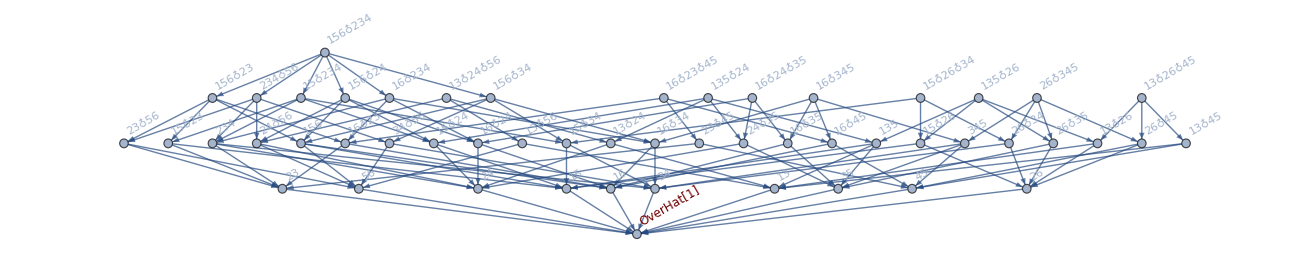

```mathematica
FormulaGraphReverse[allGraphs6[5316627,"colofour"]]
```

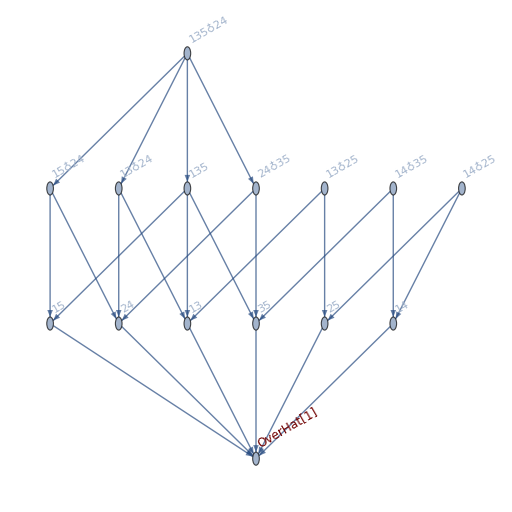

```mathematica
FormulaGraphReverse[allGraphs5[19936,"colofour"]]
```

```mathematica
allGraphs5[19936,"colofour"]/.RepGraph["C"]
```

-Graphics-368980+-Graphics-361660+-Graphics-368170+-Graphics-361120+-Graphics-303340+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-302530+-Graphics-295510+-Graphics-295270+-Graphics-295240

```mathematica
allGraphs5[starKey,"colofour"]/.RepGraph["C"]
```

-Graphics-492161+-Graphics-492081+-Graphics-304961+-Graphics-297681+-Graphics-302621+-Graphics-492070+-Graphics-297670+-Graphics-295330+-Graphics-302530+-Graphics-295250+-Graphics-295240

```mathematica
IntegerDigits[starKey,3]
```

{1,1,0,0,1,1,0,1,0}

```mathematica
IntegerDigits[starKey,3]
```

```mathematica
allGraphs5[starKey,"matrix"]//MatrixForm
```

(2 | 0 | 1 | 1 | 0
0 | 2 | 0 | 1 | 1
1 | 0 | 2 | 0 | 1
1 | 1 | 0 | 2 | 0
0 | 1 | 1 | 0 | 2)

```mathematica
allGraphs5[starKey,"matrix"]
```

{{2,0,1,1,0},{0,2,0,1,1},{1,0,2,0,1},{1,1,0,2,0},{0,1,1,0,2}}

```mathematica
{{2,0,1,1,0,0},{0,2,0,1,1,0},{1,0,2,0,1,1},{1,1,0,2,0,1},{0,1,1,0,2,1},{0,0,1,1,1,2}}//GraphMatrixSignature
```

2134624

```mathematica
allGraphs6[2134624,"graph"]
```

-Graphics-